# Numerical results for optimum voting rule selection

This notebook compares the predicted optimum voting rule with the numerically computed optimum voting rule.

### Copyright notice

Copyright (C) 2012 Donagh Horgan.
Email: donaghh@rennes.ucc.ie.

This program is free software : you can redistribute it and/or modify
it under the terms of the GNU General Public License as published by
the Free Software Foundation, either version 3 of the License, or
(at your option) any later version.

This program is distributed in the hope that it will be useful,
but WITHOUT ANY WARRANTY; without even the implied warranty of
MERCHANTABILITY or FITNESS FOR A PARTICULAR PURPOSE. See 
COPYING for more details.

You should have received a copy of the GNU General Public License
along with this program. If not, see http://www.gnu.org/licenses.

### Version information

09/08/2012
1.0

### Changelog

Version 1.0: This version was used in the submitted version of the paper.

## Set up

Clear all symbol values and load function definitions:

```mathematica
ClearAll["Global`*"];
```

```mathematica
path=NotebookDirectory[];
SetDirectory[ToFileName[path]];
ParallelEvaluate[AppendTo[$Path,path]];
ParallelEvaluate[<<definitions.m];
<<definitions.m
<<PlotLegends`
```

## Variables

Here, we define the parameters to be used:

```mathematica
M=200;
n=20;
v=15;
δ=20;
snrdb=-10;
```

```mathematica
thresholds=Range[150,250,1];
```

```mathematica
γ=10^(snrdb/10);
```

## Calculations

Calculate the theoretical and numerical optimal voting rules:

```mathematica
theoreticalOptimumVotingRule=Table[{λ,k[{ProbabilityOfAcquisition[M,λ],1-ProbabilityOfFalseAlarm[M,λ+δ]-ProbabilityOfAcquisition[M,λ],ProbabilityOfFalseAlarm[M,λ+δ]},{ProbabilityOfMissedDetection[M,γ,λ],1-ProbabilityOfDetection[M,γ,λ+δ]-ProbabilityOfMissedDetection[M,γ,λ],ProbabilityOfDetection[M,γ,λ+δ]},{v,n}]},{λ,thresholds}];
```

```mathematica
numericalData=Table[FusionCenterProbabilityOfFalseAlarm[{ProbabilityOfAcquisition[M,λ],1-ProbabilityOfFalseAlarm[M,λ+δ]-ProbabilityOfAcquisition[M,λ],ProbabilityOfFalseAlarm[M,λ+δ]},v,k]+1-FusionCenterProbabilityOfDetection[{ProbabilityOfMissedDetection[M,γ,λ],1-ProbabilityOfDetection[M,γ,λ+δ]-ProbabilityOfMissedDetection[M,γ,λ],ProbabilityOfDetection[M,γ,λ+δ]},v,k]//N,{λ,thresholds},{k,v}];
numericalOptimumVotingRule=Table[Flatten[{thresholds[[i]],Position[numericalData[[i]],Min[numericalData[[i]]]]}],{i,1,Length[thresholds],5}];
```

## Results

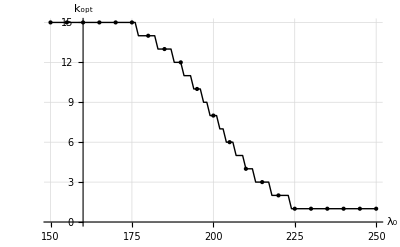

```mathematica
ListPlot[{theoreticalOptimumVotingRule,numericalOptimumVotingRule},AxesLabel->{"λ_0","k_opt"},PlotStyle->{Black,{Black,PointSize[Medium]}},Joined->{True,False},PlotLegend->{"Simulation","Theoretical"},LegendSize->{0.7,0.5},LegendPosition->{0,0},LegendShadow->None,GridLines->Automatic,ImageSize->400]
```